## Styles and custom color maps

```mathematica
width=2;
framewidth=1.5;
```

```mathematica
fixLogPlots[gr_]:=gr/.f:(Charting`ScaledTicks|Charting`ScaledFrameTicks)[{Log,Exp}]:>(Part[#,;;, ;;3]&@*f)
OpaqueBox[legend_]:=Graphics[{{White,Opacity[0.5],Rectangle[]},Inset[legend,{0.5,0.6},Center]}]
```

```mathematica
FrameTicksFontSize=20;
FrameFontSize=20;
FrameLabelSize = 12;
PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial",{AbsoluteThickness[framewidth]}],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial",{AbsoluteThickness[framewidth]}]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[framewidth]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[framewidth]]},
LabelStyle->{Directive[Black,FontSize->FrameLabelSize,FontFamily->"Arial"]},
AspectRatio->0.75,ImageSize->400,(*PlotStyle->styles,*)PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[ListLogPlot,PlotOptions];
SetOptions[ListLogLinearPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];
SetOptions[ParametricPlot,PlotOptions];
SetOptions[ListStepPlot,PlotOptions];
PlotOptions3D = {PlotStyle->Directive[Lighter[Lighter[Red]],Specularity[Orange,10],Opacity[1]],PlotPoints->60,MeshStyle->{Opacity[0.5]},Mesh->16,PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->14,FontFamily->"Arial"}};
SetOptions[Plot3D,PlotOptions3D];
ListPlotOptions3D = {PlotStyle->Directive[Lighter[Lighter[Red]],Specularity[Orange,10],Opacity[1]],MeshStyle->{Opacity[0.5]},Mesh->16,PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->14,FontFamily->"Arial"},ColorFunction->"SunsetColors"};
SetOptions[ListPlot3D,ListPlotOptions3D];
DensityPlotOptions = {PlotPoints->60,PlotRange->All,ColorFunction->"SunsetColors",ImageSize->Medium,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]]}};
SetOptions[DensityPlot,DensityPlotOptions];
ListDensityPlotOptions = {PlotRange->All,ColorFunction->"SunsetColors",ImageSize->Medium,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]]}};
SetOptions[ListDensityPlot,ListDensityPlotOptions];
```

```mathematica
Legending`LegendDump`$DefaultMarkerStyle=EdgeForm[Opacity[1]];
```

```mathematica
ColorHelix[z_] := Module[{start,rot,gamma,amp,angle,red,green,blue,min,max},
start=0.6;
rot=1.5;  
angle=2.0*Pi*(start/3.0+rot*z);
amp = 0.15;
red=z+amp(-0.14861 Cos[angle]+1.78277Sin[angle]);green=z+amp(-0.29227 Cos[angle]-0.90649Sin[angle]);blue=z+amp(1.97294*Cos[angle]);
RGBColor[Abs[Sqrt[1-red]],Abs[Sqrt[1-green]],Abs[Sqrt[1-blue]]]
]
```

## Definitions and Setup

```mathematica
hbarc = 0.197326938; (* GeV fm *)
```

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/Users/mstrickland/Library/CloudStorage/Dropbox/cnm-effect/qtraj

## Experimental Data for RAA (5.02 TeV)

#### CMS 5.02 TeV new 2S and 3S data; 1S comes from Phys. Lett. B 790, 270 (2019) [NEW, Jan 23 2023 update]

```mathematica
(* digitized from https://indico.cern.ch/event/895086/contributions/4716202/attachments/2423092/4147702/QM2022_upsilon_soohwanlee_final.pdf *)
```

```mathematica
newDataNpart={({{11.43, 0.790.18}, {31.21, 0.920.15}, {54.42, 0.610.08}, {87.19, 0.520.06}, {131., 0.490.04}, {188.2, 0.400.05}, {262.3, 0.3240.027}, {331.5, 0.3210.029}, {382.3, 0.3190.027}}),({{11.43, 0.600.13}, {31.21, 0.440.08}, {54.42, 0.250.05}, {87.19, 0.1770.030}, {131., 0.1310.024}, {188.2, 0.0960.022}, {262.3, 0.1000.019}, {331.5, 0.0730.021}, {382.3, 0.0780.020}}),({{11.43, 0.530.19}, {42.81, 0.290.07}, {109.1, 0.1090.035}, {269.1, 0.0510.019}})};
```

```mathematica
CMSnpartExpt5020Y1Sdata1 = newDataNpart[[1]];
CMSnpartExpt5020Y2Sdata1 = newDataNpart[[2]];
CMSnpartExpt5020Y3Sdata1 = newDataNpart[[3]];
```

```mathematica
(* QM2022 scanned version was ({{2.0, 0.0466244725738397±0.022027829918767006}, {6.5, 0.0521097046413502±0.023682437310487595}, {12.0, 0.060337552742616±0.018200681308926006}, {22.5, 0.0850210970464135±0.020428839582230504}})*)
```

```mathematica
newDataPT ={({{1., 0.300.13}, {3., 0.360.05}, {5., 0.390.05}, {7.5, 0.400.04}, {10.5, 0.420.06}, {21., 0.430.04}}),({{1.5, 0.0870.019}, {4.5, 0.1220.019}, {7.5, 0.0980.021}, {12., 0.1260.021}, {22.5, 0.1400.022}}),({{2., 0.0650.030}, {6.5, 0.0670.030}, {12., 0.0690.032}, {22.5, 0.1000.026}})}
```

{{{1.,0.300.13},{3.,0.360.05},{5.,0.390.05},{7.5,0.400.04},{10.5,0.420.06},{21.,0.430.04}},{{1.5,0.0870.019},{4.5,0.1220.019},{7.5,0.0980.021},{12.,0.1260.021},{22.5,0.1400.022}},{{2.,0.0650.030},{6.5,0.0670.030},{12.,0.0690.032},{22.5,0.1000.026}}}

```mathematica
CMSnpartExpt5020Y1Sdata1pt=newDataPT[[1]]
CMSnpartExpt5020Y2Sdata1pt=newDataPT[[2]]
CMSnpartExpt5020Y3Sdata1pt=newDataPT[[3]]
```

{{1.,0.300.13},{3.,0.360.05},{5.,0.390.05},{7.5,0.400.04},{10.5,0.420.06},{21.,0.430.04}}

{{1.5,0.0870.019},{4.5,0.1220.019},{7.5,0.0980.021},{12.,0.1260.021},{22.5,0.1400.022}}

{{2.,0.0650.030},{6.5,0.0670.030},{12.,0.0690.032},{22.5,0.1000.026}}

```mathematica
cmsPTint1S=Interpolation[CMSnpartExpt5020Y1Sdata1pt]
cmsPTint2S=Interpolation[CMSnpartExpt5020Y2Sdata1pt]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
ptBins = {2.52.5,8.53.5,21.9.};
ptVals  = {2.5,8.5,21.};
```

```mathematica
pt2S1Srat=(cmsPTint2S/@ptVals)/(cmsPTint1S/@ptVals);
Transpose[{ptBins,pt2S1Srat}]
```

{{2.52.5,0.310.10},{8.53.5,0.220.09},{21.9.,0.390.08}}

```mathematica
(*Clear[mapValue]
mapValue[x_]:=x["Value"]*)
```

```mathematica
(*temp= {{ Around[(0+5)/2,(5-0)/2], Around[0.32,0.1]},{ Around[(5+12)/2,(12-5)/2],Around[0.244,0.083]},{ Around[(12+30)/2,(30-12)/2], Around[0.374,0.081]}};
temp[[All,1]]*)
```

#### ALICE 5.02 TeV data from Phys. Lett. B 790, 89 (2019)

```mathematica
ALICEnpartExpt5020Y1S={{{27.01,0.600000},{0.1,0.04}},{{108.6,0.5},{0.05,0.03}},{{223.5,0.35},{0.03,0.02}},{{355.7,0.34},{0.03,0.02}}};
```

```mathematica
pointMap2[x_] := {x[[1,1]],Around[x[[1,2]],Sqrt[x[[2,1]]]^2+x[[2,2]]^2]}
```

```mathematica
ALICEnpartExpt5020Y1Sdata1 = pointMap2 /@ ALICEnpartExpt5020Y1S
```

{{27.01,0.600.10},{108.6,0.500.05},{223.5,0.3500.030},{355.7,0.3400.030}}

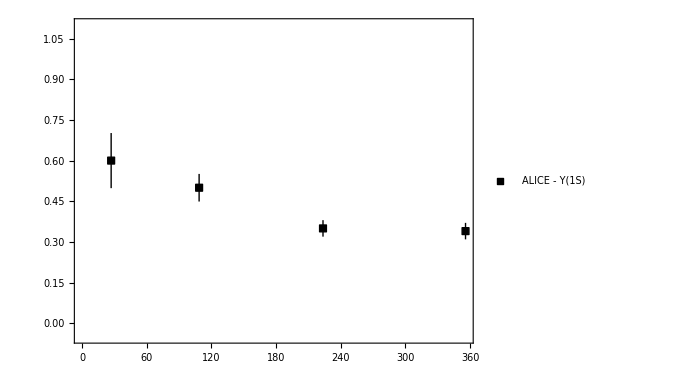

```mathematica
y1sALICEPlot=ListPlot[ALICEnpartExpt5020Y1Sdata1,(*PlotStyle->styles[[1]],*)IntervalMarkersStyle->Black,PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Rectangle[]},ImageSize->7]},ImageSize->500,PlotRange->{-0.05,1.1},PlotLegends->Placed[LineLegend[{"ALICE - Y(1S)"},LabelStyle->18],{0.8,0.85}]]
```

```mathematica
ALICEptExpt5020Y1S={{{1,0.37},{0.04,0.05}},{{3,0.41},{0.03,0.03}},{{5,0.38},{0.04,0.05}},{{10.5,0.45},{0.04,0.05}}};
```

```mathematica
ALICEptExpt5020Y1Sdata1 = pointMap2 /@ ALICEptExpt5020Y1S
```

{{1,0.370.04},{3,0.4100.031},{5,0.380.04},{10.5,0.450.04}}

```mathematica
ALICEptExpt5020Y1S={{{1.0,0.345},{0.031,0.04}},
{{3.0,0.387},{0.022,0.035}},
{{5.0,0.345},{0.021,0.026}},
{{7.5,0.298},{0.027,0.039}},
{{12.0,0.364},{0.044,0.065}}}
```

{{{1.,0.345},{0.031,0.04}},{{3.,0.387},{0.022,0.035}},{{5.,0.345},{0.021,0.026}},{{7.5,0.298},{0.027,0.039}},{{12.,0.364},{0.044,0.065}}}

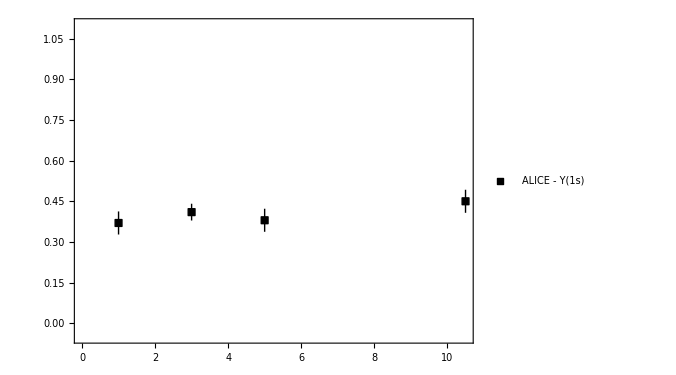

```mathematica
ptALICEPlot=ListPlot[ALICEptExpt5020Y1Sdata1,(*PlotStyle->styles[[1]],*)IntervalMarkersStyle->Black,PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Rectangle[]},ImageSize->7]},ImageSize->500,PlotRange->{-0.05,1.1},PlotLegends->Placed[LineLegend[{"ALICE - Y(1s)"},LabelStyle->18],{0.75,0.7}]]
```

#### ALICE 5.02 TeV data from 2011.05758

```mathematica
ALICEraaC = {{11.761584 ,0.8641449},
{42.445614 ,0.45022938},
{87, 0.45482674},
{131.4, 0.4100887},
{189.2, 0.4003135},
{241.15063 ,0.31416014},
{282.78186, 0.32513508},
{333.3 ,0.3360841},
{384.3,0.3151856}};
```

```mathematica
ALICEraaSys ={0.94372195,
0.47251055,
0.47870088,
0.42600524,
0.42577913,
0.33962578,
0.33786717,
0.35836527,
0.33110362}-ALICEraaC[[All,2]];
```

```mathematica
ALICEraaStat = 
{1.0344381,
0.5059323,
0.50416505,
0.44351333,
0.42896217,
0.34758332,
0.3505993,
0.36632285,
0.34224275}-ALICEraaC[[All,2]];
```

```mathematica
mapPoint[x_] := Around[x[[1]],x[[2]]]
```

```mathematica
ALICEnpartExpt5020Y1Sdata1=Transpose[{ALICEraaC[[All,1]],mapPoint/@Transpose[{ALICEraaC[[All,2]],Sqrt[ALICEraaSys^2 + ALICEraaStat^2]}]}]
```

{{11.7616,0.860.19},{42.4456,0.450.06},{87,0.450.05},{131.4,0.410.04},{189.2,0.400.04},{241.151,0.310.04},{282.782,0.3250.028},{333.3,0.340.04},{384.3,0.3150.031}}

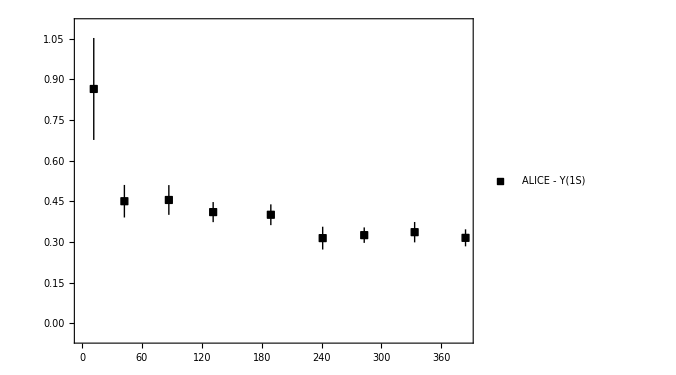

```mathematica
y1sALICEPlot=ListPlot[ALICEnpartExpt5020Y1Sdata1,(*PlotStyle->styles[[1]],*)IntervalMarkersStyle->Black,PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Rectangle[]},ImageSize->7]},ImageSize->500,PlotRange->{-0.05,1.1},PlotLegends->Placed[LineLegend[{"ALICE - Y(1S)"},LabelStyle->18],{0.8,0.85}]]
```

```mathematica
(* 2s

53.98345 0.2273716
268.98068 0.103969656
54.351997 0.2592004
268.9856 0.12784234
54.35691 0.28307307
268.6236 0.12784378

*)
```

```mathematica
ALICEraaC = {{53.98345, 0.2273716},
{268.98068 ,0.103969656}};
```

```mathematica
ALICEraaSys ={0.2592004,0.12784234}-ALICEraaC[[All,2]];
```

```mathematica
ALICEraaStat = {0.28307307,0.12784378}-ALICEraaC[[All,2]];
```

```mathematica
mapPoint[x_] := Around[x[[1]],x[[2]]]
```

```mathematica
ALICEnpartExpt5020Y2Sdata1=Transpose[{ALICEraaC[[All,1]],mapPoint/@Transpose[{ALICEraaC[[All,2]],Sqrt[ALICEraaSys^2 + ALICEraaStat^2]}]}]
```

{{53.9835,0.230.06},{268.981,0.1040.034}}

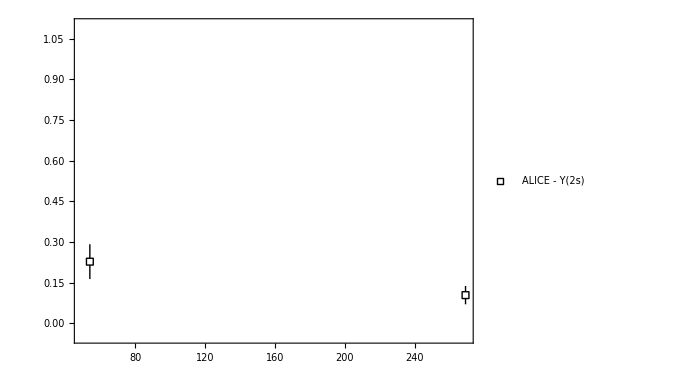

```mathematica
y2sALICEPlot=ListPlot[ALICEnpartExpt5020Y2Sdata1,(*PlotStyle->styles[[1]],*)IntervalMarkersStyle->Black,PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],White,Rectangle[]},ImageSize->7]},ImageSize->500,PlotRange->{-0.05,1.1},PlotLegends->Placed[LineLegend[{"ALICE - Y(2s)"},LabelStyle->18],{0.8,0.85}]]
```

#### ATLAS data (From Wuhan quark matter talk)

```mathematica
({{8.3, 0.790.18}, {30.6, 0.920.15}, {53.9, 0.610.08}, {87., 0.520.06}, {131.4, 0.490.04}, {189.2, 0.400.05}, {264.2, 0.3240.027}, {333.3, 0.3210.029}, {384.3, 0.3190.027}})
```

{{8.3,0.790.18},{30.6,0.920.15},{53.9,0.610.08},{87.,0.520.06},{131.4,0.490.04},{189.2,0.400.05},{264.2,0.3240.027},{333.3,0.3210.029},{384.3,0.3190.027}}

```mathematica
ATLASpts1s = {{22.4492,0.790.16},{70.4292,0.520.12},{131.4,0.430.09},{189.2,0.350.07},{243.168,0.290.06},{285.471,0.270.05},{333.3,0.290.05},{384.3,0.250.05}};
```

```mathematica
ATLASpts2s ={{46.9528,0.350.14},{160.763,0.130.11},{264.2,0.080.05}}
```

{{46.9528,0.350.14},{160.763,0.130.11},{264.2,0.080.05}}

```mathematica
ATLASpts1spt={{1,0.240.13},{3,0.270.07},{5,0.310.06},{7.5,0.370.09},{10.5,0.310.06},{21,0.340.05}}
```

{{1,0.240.13},{3,0.270.07},{5,0.310.06},{7.5,0.370.09},{10.5,0.310.06},{21,0.340.05}}

```mathematica
(*xvals = Import["/Users/mstrick6/Desktop/ATLASy2spt.csv"][[7;;All]][[1;;3]][[All,1]]
pts=Import["/Users/mstrick6/Desktop/ATLASy2spt.csv"][[7;;All]][[1;;3]][[All,2]]
ptsStat = Import["/Users/mstrick6/Desktop/ATLASy2spt.csv"][[7;;All]][[4;;6]][[All,2]]
ptsSys = Import["/Users/mstrick6/Desktop/ATLASy2spt.csv"][[7;;All]][[7;;9]][[All,2]]*)
```

```mathematica
(*ATLASpts2spt= Table[{xvals[[i]],Around[pts[[i]],Sqrt[(ptsStat[[i]]-pts[[i]])^2+(ptsSys[[i]]-pts[[i]])^2]]},{i,1,Length[xvals]}]*)
```

```mathematica
ATLASpts2spt={{2,0.100.09},{6.5,0.130.07},{19.5,0.100.05}}
```

{{2,0.100.09},{6.5,0.130.07},{19.5,0.100.05}}

#### Combined ALICE, ATLAS, and CMS data

```mathematica
ALICEnpartExpt5020Y1Sdata1
```

{{11.7616,0.860.19},{42.4456,0.450.06},{87,0.450.05},{131.4,0.410.04},{189.2,0.400.04},{241.151,0.310.04},{282.782,0.3250.028},{333.3,0.340.04},{384.3,0.3150.031}}

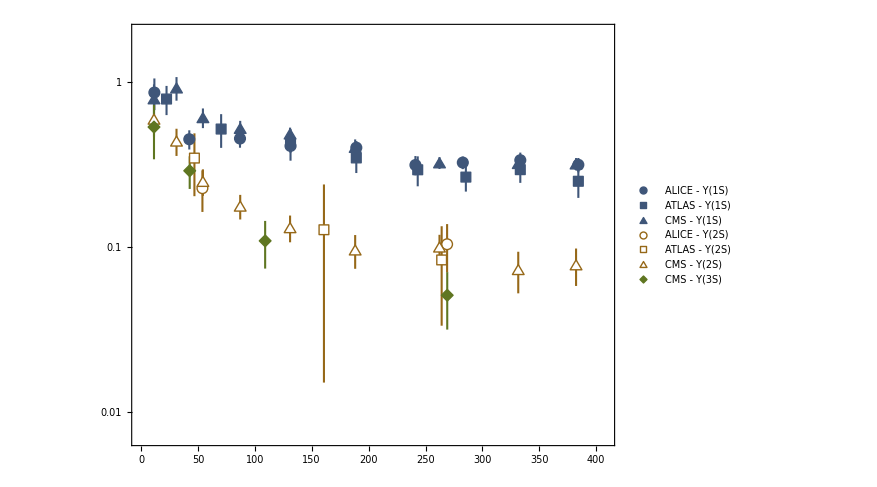

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]]//Darker;
plotColor2= ColorData[97,"ColorList"][[2]]//Darker;
plotColor3= ColorData[97,"ColorList"][[3]]//Darker;
nPartExpPlot =ListLogPlot[{ALICEnpartExpt5020Y1Sdata1,ATLASpts1s,CMSnpartExpt5020Y1Sdata1,ALICEnpartExpt5020Y2Sdata1,ATLASpts2s,CMSnpartExpt5020Y2Sdata1,CMSnpartExpt5020Y3Sdata1},IntervalMarkersStyle->{{AbsoluteThickness[1.5],plotColor1},{AbsoluteThickness[1.5],plotColor1},{AbsoluteThickness[1.5],plotColor1},{AbsoluteThickness[1.5],plotColor2},{AbsoluteThickness[1.5],plotColor2},{AbsoluteThickness[1.5],plotColor2},{AbsoluteThickness[1.5],plotColor3}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor1}],plotColor1,Disk[]},ImageSize->11],
Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor1}],plotColor1,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor1}],plotColor1,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->12],
Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],White,Disk[]},ImageSize->11],
Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],White,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],White,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->12],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor3}],plotColor3,Polygon[{{1,0},{0,1},{-1,0},{0,-1}}]},ImageSize->12]},ImageSize->650,PlotLegends->Placed[LineLegend[{"ALICE - Y(1S)","ATLAS - Y(1S)","CMS - Y(1S)","ALICE - Y(2S)","ATLAS - Y(2S)","CMS - Y(2S)","CMS - Y(3S)"},LabelStyle->16,LegendLayout->{"Column",3},LegendMargins->{0,0},LegendMarkerSize->11],{0.63,0.88}],PlotRange->{{0,408},{0.007,2}}]
```

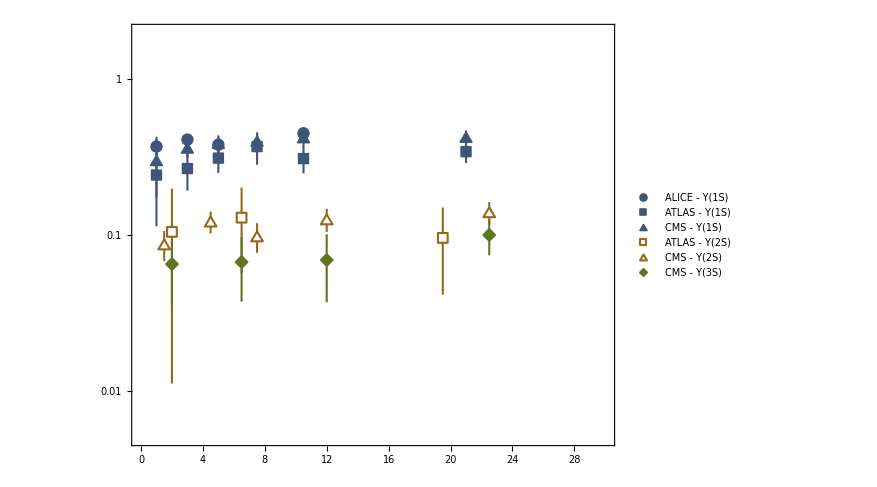

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]]//Darker;
plotColor2= ColorData[97,"ColorList"][[2]]//Darker;
plotColor3= ColorData[97,"ColorList"][[3]]//Darker;
ptExpPlot=ListPlot[{ALICEptExpt5020Y1Sdata1,ATLASpts1spt,CMSnpartExpt5020Y1Sdata1pt,ATLASpts2spt,CMSnpartExpt5020Y2Sdata1pt,CMSnpartExpt5020Y3Sdata1pt},IntervalMarkersStyle->{{AbsoluteThickness[1.5],plotColor1},{AbsoluteThickness[1.5],plotColor1},{AbsoluteThickness[1.5],plotColor1},{AbsoluteThickness[1.5],plotColor2},{AbsoluteThickness[1.5],plotColor2},{AbsoluteThickness[1.5],plotColor3}},ScalingFunctions->{None,"Log"},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1.2],plotColor1}],plotColor1,Disk[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1.2],plotColor1}],plotColor1,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1.2],plotColor1}],plotColor1,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->12],
Graphics[{EdgeForm[{AbsoluteThickness[1.5],plotColor2}],White,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1.5],plotColor2}],White,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->12],Graphics[{EdgeForm[{AbsoluteThickness[1.5],plotColor3}],plotColor3,Polygon[{{1,0},{0,1},{-1,0},{0,-1}}]},ImageSize->12
]},ImageSize->650,PlotLegends->Placed[LineLegend[{"ALICE - Y(1S)","ATLAS - Y(1S)","CMS - Y(1S)","ATLAS - Y(2S)","CMS - Y(2S)","CMS - Y(3S)"},LabelStyle->16,LegendLayout->{"Column",3},LegendMargins->{0,0},LegendMarkerSize->11],{0.38,0.89}],PlotRange->{{0,30},{0.005,2}}]
```

#### Rapidity dependence

```mathematica
data1sCMS = {{0.2,0.383±0.03720215047547654},{0.6000000000000001,0.382±0.03538361202590826},{1.,0.394±0.04750789408087881},{1.4,0.362±0.042449970553582246},{1.8,0.378±0.04440720662234903},{2.2,0.415±0.09548298277703729}};
data2sCMS = {{0.4,0.111±0.03162277660168379},{1.2000000000000002,0.13±0.04743416490252569},{2.,0.07±0.05314132102234569}};
data1sALICE = {{2.65,0.433±0.06981403870282825},{2.95,0.396±0.04272001872658766},{3.2,0.398±0.05021951811795888},{3.45,0.338±0.04606517122512409},{3.8,0.305±0.05768882040742383}};

data2sALICE = {{2.9,0.081±0.04459820624195552},{3.65,0.197±0.05315072906367325}};
```

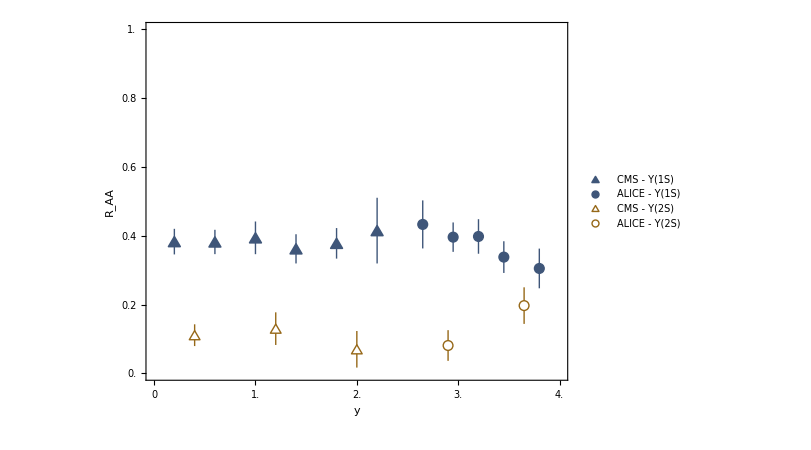

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]]//Darker;
plotColor2= ColorData[97,"ColorList"][[2]]//Darker;
CMS1S=ListPlot[data1sCMS,PlotStyle->plotColor1,IntervalMarkersStyle->plotColor1,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1.2],plotColor1}],plotColor1,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->12],PlotRange->{{0,4.0},{0,1}},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"CMS - Y(1S)"},LabelStyle->18],{0.79,0.90}],ImageSize->500];
ALICE1S=ListPlot[data1sALICE ,PlotStyle->plotColor1,IntervalMarkersStyle->plotColor1,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor1}],plotColor1,Disk[]},ImageSize->10],PlotRange->{{0,4.0},{0,1}},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"ALICE - Y(1S)"},LabelStyle->18],{0.8,0.85}],ImageSize->500];
CMS2S=ListPlot[data2sCMS,PlotStyle->plotColor2,IntervalMarkersStyle->plotColor2,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],White,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->11],PlotRange->{{0,4.0},{0,1}},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"CMS - Y(2S)"},LabelStyle->18],{0.79,0.80}],ImageSize->500];
ALICE2S=ListPlot[data2sALICE ,PlotStyle->plotColor2,IntervalMarkersStyle->plotColor2,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],White,Disk[]},ImageSize->10],PlotRange->{{0,4.0},{0,1}},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"ALICE - Y(2S)"},LabelStyle->18],{0.8,0.75}],ImageSize->500];
expPlotY=Show[{CMS1S,ALICE1S,CMS2S,ALICE2S},ImageSize->600]
```

#### Rapidity dependence (Log Scale)

```mathematica
data1sCMS = {{0.2,0.383±0.03720215047547654},{0.6000000000000001,0.382±0.03538361202590826},{1.,0.394±0.04750789408087881},{1.4,0.362±0.042449970553582246},{1.8,0.378±0.04440720662234903},{2.2,0.415±0.09548298277703729}};
data2sCMS = {{0.4,0.111±0.03162277660168379},{1.2000000000000002,0.13±0.04743416490252569},{2.,0.07±0.05314132102234569}};
data1sALICE = {{2.65,0.433±0.06981403870282825},{2.95,0.396±0.04272001872658766},{3.2,0.398±0.05021951811795888},{3.45,0.338±0.04606517122512409},{3.8,0.305±0.05768882040742383}};

data2sALICE = {{2.9,0.081±0.04459820624195552},{3.65,0.197±0.05315072906367325}};
```

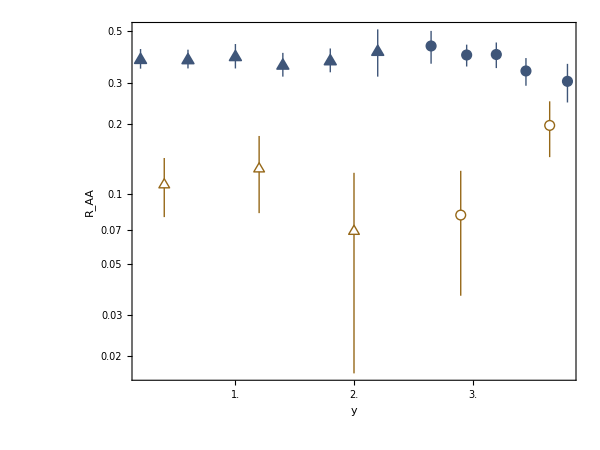

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]]//Darker;
plotColor2= ColorData[97,"ColorList"][[2]]//Darker;
CMS1S=ListLogPlot[data1sCMS,PlotStyle->plotColor1,IntervalMarkersStyle->plotColor1,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1.2],plotColor1}],plotColor1,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->12],PlotRange->{{0,4.0},Automatic},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"CMS - Y(1S)"},LabelStyle->16,LegendMargins->{10,-2}],{Left,Bottom}],ImageSize->500];
ALICE1S=ListLogPlot[data1sALICE ,PlotStyle->plotColor1,IntervalMarkersStyle->plotColor1,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor1}],plotColor1,Disk[]},ImageSize->10],PlotRange->{{0,4.0},Automatic},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"ALICE - Y(1S)"},LabelStyle->16,LegendMargins->{10,-2}],{Left,Bottom}],ImageSize->500];
CMS2S=ListLogPlot[data2sCMS,PlotStyle->plotColor2,IntervalMarkersStyle->plotColor2,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],White,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->11],PlotRange->{{0,4.0},Automatic},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"CMS - Y(2S)"},LabelStyle->16,LegendMargins->{10,-2}],{Left,Bottom}],ImageSize->500];
ALICE2S=ListLogPlot[data2sALICE ,PlotStyle->plotColor2,IntervalMarkersStyle->plotColor2,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],White,Disk[]},ImageSize->10],PlotRange->{{0,4.0},Automatic},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"ALICE - Y(2S)"},LabelStyle->16,LegendMargins->{10,-2}],{Left,Bottom}],ImageSize->500];
expPlotYLog=Show[{CMS1S,ALICE1S,CMS2S,ALICE2S},PlotRange->All,ImageSize->600]
```

## Data files

```mathematica
dataDir = "run-pa-5.02-1";
```

```mathematica
labelMap = Association[
{"run-pa-5.02-1"->  "pA; κ̂ = 6, γ̂ = 0, T_F = 190 MeV, τ_med = 0.6 fm; 5.02 TeV; runs_20240110_5172"}
];
```

```mathematica
keys=Keys[labelMap];
figureNameMap=Table[keys[[i]]->keys[[i]],{i,1,Length[keys]}]//Association
```

<|run-pa-5.02-1→run-pa-5.02-1|>

```mathematica
datafile = "/input-jumps/"<>dataDir<>"/datafile-avg.gz";
```

```mathematica
dirName = wd<>"/output-jumps/"<>figureNameMap[dataDir];
If[!DirectoryQ[dirName ],CreateDirectory[dirName]];
```

## Read in data

```mathematica
mapData[x_] := {x[[1]],Join[Table[ x[[2]][[i]],{i,1,12,2}],{x[[2,-1]]}],x[[2,-2]]}
```

```mathematica
rawDataAll=mapData/@Partition[Import[wd<>datafile,"Table"],2];
Length[rawDataAll]
```

86314

```mathematica
selectL[lval_]:=Select[rawDataAll,#[[2,7]]==lval&]
```

```mathematica
rawDataS = selectL[0];
Length[rawDataS]
rawDataP = selectL[1];
Length[rawDataP]
```

43157

43157

```mathematica
myR = RandomInteger[{1,Length[rawDataS]}]
rawDataS[[myR ]]
rawDataP[[myR ]]
```

41146

{{4.70318,0.91012,0.391404,-2.71896,9.24167,2.44523,-2.71896},{0.339823,0.343896,3.68255×10^-6,0.337474,1.27478×10^-6,1.88922×10^-10,0},200}

{{4.70318,0.91012,0.391404,-2.71896,9.24167,2.44523,-2.71896},{5.5212×10^-7,6.89665×10^-8,1.65873×10^-6,2.04302×10^-8,1.61398×10^-6,3.14841×10^-11,1},200}

```mathematica
sData=Transpose[{rawDataS[[All,2,1]], rawDataS[[All,2,2]], rawDataP[[All,2,3]], rawDataS[[All,2,4]], rawDataP[[All,2,5]], rawDataS[[All,2,6]], rawDataS[[All,3]]}];
mData = rawDataS[[All,1]];
rawData = Transpose[{mData,sData}];
```

```mathematica
bVals=rawData[[All,1,1]]//Union
```

{4.70318}

## Primordial cross sections and branching (feed down) matrix

```mathematica
splitHyperfine[x_] := {x[[1]],x[[2]],x[[3]],x[[3]],x[[3]],x[[4]],x[[5]],x[[5]],x[[5]]}
```

#### From PDG for Upsilon states

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 *)
```

```mathematica
decayMatrix= {
{1,0,0,0,0,0,0,0,0}, (* 1S *)
{0.2645,1,0,0,0,0,0,0,0}, (* 2S *)
{0.0194,0,1,0,0,0,0,0,0}, (* χb0(1P) *)
{0.352,0,0,1,0,0,0,0,0}, (* χb1(1P) *)
{0.18,0,0,0,1,0,0,0,0}, (* χb2(1P) *)
{0.0657,0.106,0,0,0,1,0,0,0}, (* 3S *)
{0.0038,0.0138,0,0,0,0,1,0,0}, (* χb0(2P) *)
{0.1153,0.181,0,0.0091,0,0,0,1,0}, (* χb1(2P) *)
{0.077,0.089,0,0,0.0051,0,0,0,1}(* χb2(2P) *)
} ;
```

```mathematica
feeddownMatrix = Transpose[decayMatrix];
MatrixForm[feeddownMatrix]
```

(1 | 0.2645 | 0.0194 | 0.352 | 0.18 | 0.0657 | 0.0038 | 0.1153 | 0.077
0 | 1 | 0 | 0 | 0 | 0.106 | 0.0138 | 0.181 | 0.089
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.0091 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.0051
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

#### LHC 5 TeV pp

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 - Extrapolated to 5 TeV *) sigmasEXP = {57.6,19,3.72,13.69,16.1,6.8,3.27,12.0,14.15}
```

{57.6,19,3.72,13.69,16.1,6.8,3.27,12.,14.15}

```mathematica
sigmas = Inverse[feeddownMatrix].sigmasEXP
```

{43.0147,14.8027,3.72,13.5808,16.0278,6.8,3.27,12.,14.15}

#### Compute 1S branching fractions and check sum rule

```mathematica
plucker1s = Table[If[i==j && i==1,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];plucker2s = Table[If[i==j && i==2,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker1p = Table[If[i==j && i≥3 && i ≤5,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker3s = Table[If[i==j && i==6,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker2p = Table[If[i==j && i≥7 && i ≤9,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
```

```mathematica
(feeddownMatrix.plucker1s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.746783

```mathematica
(feeddownMatrix.plucker2s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.0679743

```mathematica
(feeddownMatrix.plucker1p.sigmas)[[1]]/sigmasEXP[[1]]
```

0.134334

```mathematica
(feeddownMatrix.plucker3s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.00775625

```mathematica
(feeddownMatrix.plucker2p.sigmas)[[1]]/sigmasEXP[[1]]
```

0.0431524

```mathematica
0.7467833958680554+0.0679743142013889+0.13433367881944444+0.007756249999999999+0.043152361111111114
```

1.

## Integrated results (no feed down)

```mathematica
selectB[i_]:=Select[rawData,#[[1,1]]==bVals[[i]]&] 
rAAvsB[i_]:=selectB[i][[All,2]][[All,1;;6]] 
rAAavgVsB[i_]:=Mean[rAAvsB[i]]
rAAsdevVsB[i_] :=StandardDeviation[rAAvsB[i]]/Sqrt[Length[rAAvsB[i]]]
```

```mathematica
results=ParallelTable[Join[{bVals[[i]]},Riffle[rAAavgVsB[i],rAAsdevVsB[i]]],{i,1,Length[bVals]}]
```

{{4.70318,0.909729,0.00143031,0.830006,0.00137347,1.21474,0.0232113,0.785717,0.00138355,1.00298,0.0170594,0.0000161187,1.72822×10^-7}}

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
raa1s = pointMap/@results[[All,{1,2,3}]] ;
raa2s = pointMap/@results[[All,{1,4,5}]] ;
raa2p = pointMap/@results[[All,{1,6,7}]] ;
raa3s = pointMap/@results[[All,{1,8,9}]] ;
raa3p = pointMap/@results[[All,{1,10,11}]] ;
```

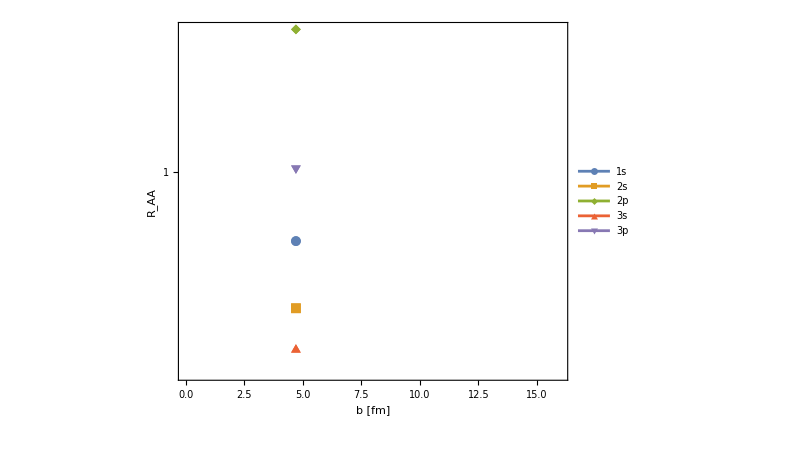

```mathematica
comp1=ListLogPlot[{raa1s,raa2s,raa2p,raa3s,raa3p},PlotRange->{{0,16},Automatic},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->{Automatic,Medium},IntervalMarkers->"Bands",FrameLabel->{"b [fm]","R_AA"},PlotLegends->Placed[LineLegend[{Style["1s",16],Style["2s",16],Style["2p",16],Style["3s",16],Style["3p",16]},LegendMarkerSize->{{60,15}}],{0.2,0.8}]]
```

## Check distribution functions

```mathematica
metaData = rawData[[All,1]];
supData = rawData[[All,2]];
```

```mathematica
ptData = metaData[[All,5]];
yData = metaData[[All,7]];
```

```mathematica
𝒟=HistogramDistribution[yData,40];
testPlot=DiscretePlot[PDF[𝒟,x],{x,-10,10,.01}];
```

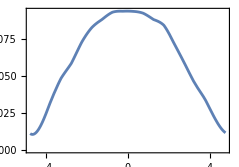
```mathematica
p1 = -Graphics-;
```

```mathematica
f[y_]:= 0.1(1- 2Sqrt[9.46^2+5^2]/5023 Cosh[y])^(13.8)
f2[y_]:= 0.1(1- Sqrt[9.46^2+15^2]/5023 Cosh[y])^(13.8)
f3[y_]:= 0.1(1- Sqrt[9.46^2+15^2]/8160 Cosh[y])^(13.8)
```

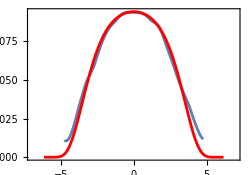

```mathematica
p2=Plot[{f[y](*,f2[y],f3[y]*)},{y,-7,7},PlotStyle->{Blue,Green,Red}];
Show[p1,p2,PlotRange->{{-7,7},All},ImageSize->250]
```

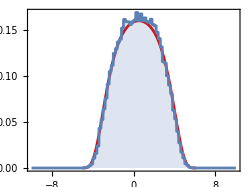

```mathematica
p3=Plot[1.7f[-y+0.5],{y,-5,6.1},PlotStyle->2];
Show[p3,testPlot,ImageSize->250]
```

## Results as a function of p_T averaged over centrality (with feed down)

```mathematica
getWeight[x_] := 1
```

```mathematica
mapWithWeight[x_] :=Join[  splitHyperfine[ x[[2]][[1;;6]] ],{x[[2,7]]}]
```

```mathematica
(*selectWeights[ptmin_,ptmax_]:=getWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax&] *)
```

```mathematica
(*selectPTweighted[ptmin_,ptmax_]:=mapWithWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax&]*)
```

```mathematica
selectWeights[ptmin_,ptmax_]:=getWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax && #[[1,7]]≥ymin&&#[[1,7]]<=ymax&]
```

```mathematica
selectPTweighted[ptmin_,ptmax_]:=mapWithWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax&& #[[1,7]]≥ymin&&#[[1,7]]<=ymax&]
```

```mathematica
weightedList[ptmin_,ptmax_]:=Module[{wtm,res},
wtm = Mean[selectWeights[ptmin,ptmax]];
res=selectPTweighted[ptmin,ptmax];
MapThread[Append,{res[[All,1;;9]]/wtm,res[[All,-1]]}]
]
```

```mathematica
nAAavgVsPT[ptmin_,ptmax_]:= Module[{wl,num,qweights},
wl=weightedList[ptmin,ptmax];
qweights = wl[[All,-1]];
num = qweights //Total;
Transpose[wl[[All,1;;9]]].qweights/num
]
```

```mathematica
nAAsdevVsPT[ptmin_,ptmax_]:=Module[{wl},
wl = weightedList[ptmin,ptmax];
StandardDeviation[wl]/Sqrt[Length[wl]]
]
nAAVsPT[ptmin_,ptmax_]:=Module[{avg,err},
avg = nAAavgVsPT[ptmin,ptmax];
err= nAAsdevVsPT[ptmin,ptmax];
Table[Around[avg[[i]],err[[i]]]sigmas[[i]],{i,1,9}]
]
```

### -1.93 < y < 1.93

```mathematica
ymin = -1.93;
ymax = 1.93;
```

```mathematica
binwidth=2.5;
ptmax = 30;
naavsptData=ParallelTable[Join[{x+binwidth/2},feeddownMatrix.nAAVsPT[x,x+binwidth]/feeddownMatrix.sigmas],{x,0,ptmax-binwidth,binwidth}]//N
```

{{1.25,0.9200.008,0.8120.008,1.220.07,1.220.07,1.220.07,0.7240.004,0.960.05,0.960.05,0.960.05},{3.75,0.9300.006,0.8250.006,1.190.06,1.190.06,1.190.06,0.74580.0031,0.950.04,0.950.04,0.950.04},{6.25,0.9400.008,0.8380.007,1.220.07,1.210.07,1.220.07,0.7580.004,0.980.05,0.980.05,0.980.05},{8.75,0.9460.011,0.8490.010,1.240.10,1.240.10,1.240.10,0.7650.005,1.020.07,1.020.07,1.020.07},{11.25,0.9710.015,0.8750.014,1.300.13,1.300.13,1.300.13,0.7860.007,1.080.10,1.080.10,1.080.10},{13.75,0.9330.020,0.8390.019,1.180.19,1.180.18,1.180.18,0.7700.010,0.960.13,0.960.13,0.960.13},{16.25,0.9810.023,0.8800.023,1.350.21,1.350.20,1.350.20,0.7900.014,1.100.15,1.100.15,1.100.15},{18.75,0.9360.028,0.8480.028,1.070.25,1.070.24,1.070.24,0.7910.019,0.930.18,0.930.18,0.930.18},{21.25,1.020.05,0.930.05,1.60.5,1.60.5,1.60.5,0.8020.024,1.40.4,1.40.4,1.40.4},{23.75,1.000.06,0.880.05,1.60.5,1.60.5,1.60.5,0.7770.028,1.20.4,1.20.4,1.20.4},{26.25,1.030.08,0.930.08,1.60.7,1.60.7,1.60.7,0.810.04,1.30.5,1.30.5,1.30.5},{28.75,1.030.05,0.960.06,1.20.4,1.20.4,1.20.4,0.900.04,1.140.35,1.140.35,1.140.35}}

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
naa1s =naavsptData[[All,{1,2}]] ;
naa2s = naavsptData[[All,{1,3}]] ;
naa3s = naavsptData[[All,{1,7}]] ;
```

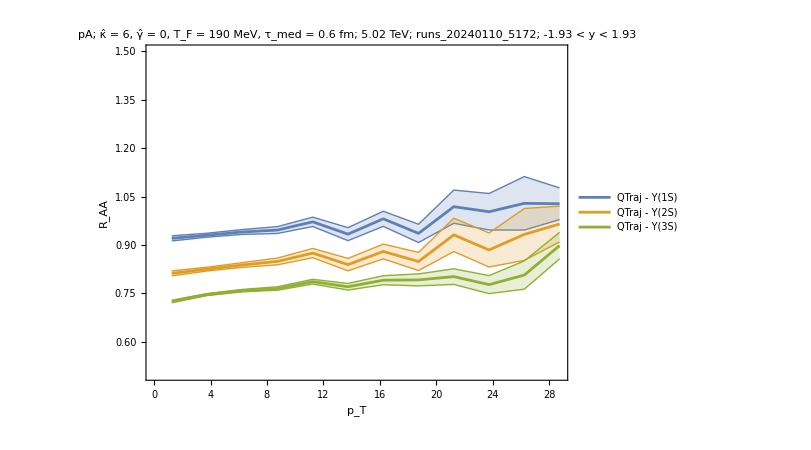

```mathematica
ptPlot=ListPlot[{naa1s,naa2s,naa3s},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"p_T","R_AA"},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotRange->{0.5,1.5},PlotLabel->labelMap[dataDir]<>"; "<>ToString[ymin]<>" < y < "<>ToString[ymax]]
```

```mathematica
fileName =dirName<>"/rpavspt-central.m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
qtrajRPAvspt={naa1s,naa2s,naa3s};
Save[fileName,qtrajRPAvspt]
```

### -5 < y < -2.5

```mathematica
ymin = -5;
ymax = -2.5;
```

```mathematica
binwidth=2.5;
ptmax = 23;
naavsptData=ParallelTable[Join[{x+binwidth/2},feeddownMatrix.nAAVsPT[x,x+binwidth]/feeddownMatrix.sigmas],{x,0,ptmax-binwidth,binwidth}]//N
```

{{1.25,0.9730.013,0.9360.014,1.150.11,1.150.11,1.150.11,0.8930.009,1.040.09,1.040.09,1.040.09},{3.75,1.0030.010,0.9690.011,1.250.09,1.250.08,1.250.08,0.9130.008,1.140.07,1.140.07,1.140.07},{6.25,0.9910.013,0.9540.014,1.130.11,1.130.11,1.130.11,0.9190.010,1.040.09,1.040.09,1.040.09},{8.75,0.9830.020,0.9500.023,1.310.17,1.310.17,1.310.17,0.8750.015,1.210.15,1.210.15,1.210.15},{11.25,0.9870.030,0.9530.032,1.040.24,1.040.24,1.040.24,0.9350.023,0.960.20,0.960.20,0.960.20},{13.75,1.200.10,1.160.11,2.20.9,2.20.9,2.20.9,0.960.05,2.00.8,2.00.8,2.00.8},{16.25,0.910.05,0.870.06,0.70.4,0.70.4,0.70.4,0.910.05,0.640.33,0.640.33,0.640.33},{18.75,0.800.06,0.780.06,0.450.20,0.450.19,0.450.20,0.840.07,0.450.20,0.450.20,0.450.20},{21.25,0.680.07,0.630.07,0.040.04,0.040.04,0.040.04,0.740.09,0.050.05,0.050.05,0.050.05}}

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
naa1s =naavsptData[[All,{1,2}]] ;
naa2s = naavsptData[[All,{1,3}]] ;
naa3s = naavsptData[[All,{1,7}]] ;
```

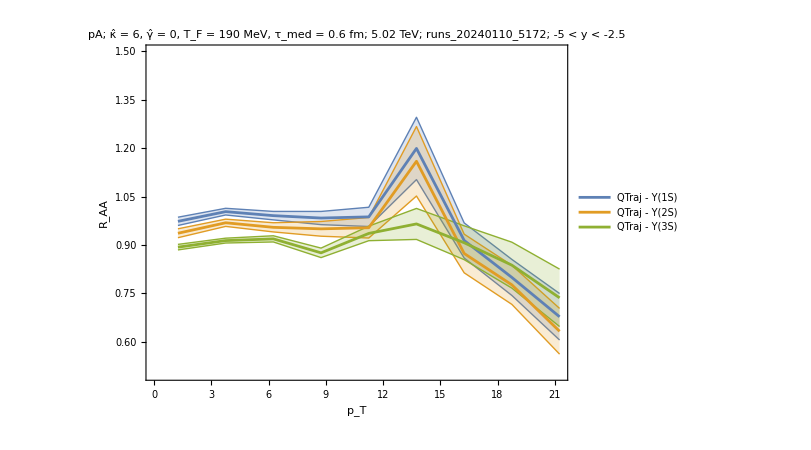

```mathematica
ptPlot=ListPlot[{naa1s,naa2s,naa3s},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"p_T","R_AA"},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotRange->{0.5,1.5},PlotLabel->labelMap[dataDir]<>"; "<>ToString[ymin]<>" < y < "<>ToString[ymax]]
```

```mathematica
fileName =dirName<>"/rpavspt-backward.m";
qtrajRPAvspt={naa1s,naa2s,naa3s};
Save[fileName,qtrajRPAvspt]
```

### 1.5 < y < 4

```mathematica
ymin = 1.5;
ymax = 4;
```

```mathematica
binwidth=2.5;
ptmax = 23;
naavsptData=ParallelTable[Join[{x+binwidth/2},feeddownMatrix.nAAVsPT[x,x+binwidth]/feeddownMatrix.sigmas],{x,0,ptmax-binwidth,binwidth}]//N
```

{{1.25,0.9110.009,0.8230.009,1.040.08,1.040.08,1.040.08,0.7680.005,0.860.06,0.860.06,0.860.06},{3.75,0.9420.008,0.8510.008,1.180.07,1.180.07,1.180.07,0.7800.004,0.970.05,0.970.05,0.970.05},{6.25,0.9370.009,0.8530.009,1.140.08,1.130.08,1.130.08,0.7890.005,0.950.06,0.950.06,0.950.06},{8.75,0.9700.015,0.8840.014,1.340.13,1.330.13,1.340.13,0.7960.008,1.110.10,1.110.10,1.110.10},{11.25,0.9770.021,0.8910.021,1.350.20,1.350.19,1.350.20,0.8050.011,1.110.14,1.110.14,1.110.14},{13.75,0.9510.025,0.8760.025,1.190.22,1.190.22,1.190.22,0.8100.016,1.030.17,1.030.17,1.030.17},{16.25,1.060.05,0.950.05,1.90.5,1.90.5,1.90.5,0.7760.020,1.60.4,1.60.4,1.60.4},{18.75,0.910.04,0.840.04,0.930.31,0.930.31,0.930.31,0.7980.027,0.830.27,0.830.27,0.830.27},{21.25,0.910.06,0.850.07,1.20.6,1.20.6,1.20.6,0.760.04,1.10.5,1.10.5,1.10.5}}

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
naa1s =naavsptData[[All,{1,2}]] ;
naa2s = naavsptData[[All,{1,3}]] ;
naa3s = naavsptData[[All,{1,7}]] ;
```

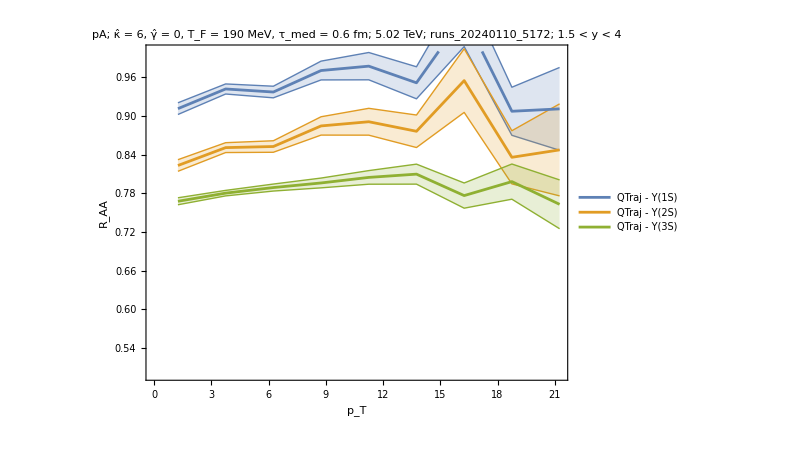

```mathematica
ptPlot=ListPlot[{naa1s,naa2s,naa3s},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"p_T","R_AA"},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotRange->{0.5,1},PlotLabel->labelMap[dataDir]<>"; "<>ToString[ymin]<>" < y < "<>ToString[ymax]]
```

```mathematica
fileName =dirName<>"/rpavspt-forward.m";
qtrajRPAvspt={naa1s,naa2s,naa3s};
Save[fileName,qtrajRPAvspt]
```

## Results as a function of y averaged over centrality and p_T (with feed down)

#### Setup

```mathematica
getWeight[x_] := 1
```

```mathematica
mapWithWeight[x_] := Join[ splitHyperfine[ x[[2]][[1;;6]] ],{x[[2,7]]}]
```

```mathematica
selectWeights[ymin_,ymax_]:=getWeight/@ Select[rawData,#[[1,7]]≥ymin&&#[[1,7]]≤ymax&]
```

```mathematica
selectYweighted[ymin_,ymax_]:=mapWithWeight/@ Select[rawData,#[[1,7]]≥ymin&&#[[1,7]]≤ymax&]
```

```mathematica
weightedList[ymin_,ymax_]:=Module[{wtm,res},
wtm = Mean[selectWeights[ymin,ymax]];
res = selectYweighted[ymin,ymax];
MapThread[Append,{res[[All,1;;9]]/wtm,res[[All,-1]]}]
]
```

```mathematica
nAAavgVsY[ymin_,ymax_]:= Module[{wl,num,qweights},
wl=weightedList[ymin,ymax];
qweights = wl[[All,-1]];
num = qweights //Total;
Transpose[wl[[All,1;;9]]].qweights/num
]
```

```mathematica
nAAsdevVsY[ymin_,ymax_]:=Module[{wl},
wl = weightedList[ymin,ymax];
StandardDeviation[wl]/Sqrt[Length[wl]]
]
nAAVsY[ymin_,ymax_]:=Module[{avg,err},
avg = nAAavgVsY[ymin,ymax];
err= nAAsdevVsY[ymin,ymax];
ParallelTable[Around[avg[[i]],err[[i]]]sigmas[[i]],{i,1,9}]
]
```

#### Results

```mathematica
binwidth=0.5;
ymax =5;
(* flip y here due to inverse in hydro setup *)
naavsyData=Reverse[Table[Join[{-x+-binwidth/2},feeddownMatrix.nAAVsY[x,x+binwidth]/feeddownMatrix.sigmas],{x,-ymax,ymax-binwidth,binwidth}]//N]
```

{{-4.75,1.0180.005,1.0160.006,1.0560.028,1.0560.028,1.0560.028,1.0080.006,1.0490.027,1.0490.027,1.0490.027},{-4.25,0.9930.007,0.9830.007,1.020.04,1.020.04,1.020.04,0.9770.006,0.990.04,0.990.04,0.990.04},{-3.75,0.9930.008,0.9610.009,1.160.07,1.160.07,1.160.07,0.9220.006,1.060.06,1.060.06,1.060.06},{-3.25,0.9430.008,0.8890.009,1.080.07,1.080.07,1.080.07,0.8450.006,0.950.06,0.950.06,0.950.06},{-2.75,0.9490.010,0.8590.010,1.250.09,1.250.09,1.250.09,0.7780.005,1.020.07,1.020.07,1.020.07},{-2.25,0.9210.010,0.8160.010,1.150.09,1.150.09,1.150.09,0.7390.005,0.930.07,0.930.07,0.930.07},{-1.75,0.9250.010,0.8090.009,1.200.09,1.200.09,1.200.09,0.7240.005,0.940.06,0.940.06,0.940.06},{-1.25,0.9230.010,0.8080.009,1.200.09,1.190.09,1.190.09,0.7250.005,0.940.06,0.940.06,0.940.06},{-0.75,0.9350.010,0.8210.010,1.250.09,1.250.09,1.250.09,0.7320.005,0.980.07,0.980.07,0.980.07},{-0.25,0.9180.010,0.8140.009,1.140.09,1.140.09,1.140.09,0.7430.005,0.900.06,0.900.06,0.900.06},{0.25,0.9450.010,0.8440.009,1.280.09,1.270.09,1.270.09,0.7540.005,1.030.06,1.030.06,1.030.06},{0.75,0.9520.010,0.8560.009,1.260.09,1.260.09,1.260.09,0.7710.005,1.030.06,1.030.06,1.030.06},{1.25,0.9510.010,0.8580.010,1.260.09,1.260.09,1.260.09,0.7770.005,1.020.07,1.020.07,1.020.07},{1.75,0.9540.010,0.8730.010,1.220.09,1.220.09,1.220.09,0.7970.005,1.030.07,1.030.07,1.030.07},{2.25,0.9940.011,0.9200.011,1.390.10,1.380.10,1.380.10,0.8300.006,1.170.08,1.170.08,1.170.08},{2.75,0.9720.009,0.9260.010,1.160.08,1.160.08,1.160.08,0.8770.006,1.040.07,1.040.07,1.040.07},{3.25,1.0120.011,0.9820.012,1.270.09,1.260.09,1.270.09,0.9280.008,1.170.08,1.170.08,1.170.08},{3.75,1.0150.013,1.0050.014,1.180.09,1.180.09,1.180.09,0.9710.011,1.140.09,1.140.09,1.140.09},{4.25,1.0030.016,1.0010.017,1.080.07,1.080.07,1.080.07,0.9840.019,1.070.06,1.070.06,1.070.06},{4.75,1.0060.004,1.0060.004,1.0120.013,1.0120.013,1.0120.013,1.0040.005,1.0120.013,1.0120.013,1.0120.013}}

```mathematica
naa1s =naavsyData[[All,{1,2}]] ;
naa2s = naavsyData[[All,{1,3}]] ;
naa3s = naavsyData[[All,{1,7}]] ;
```

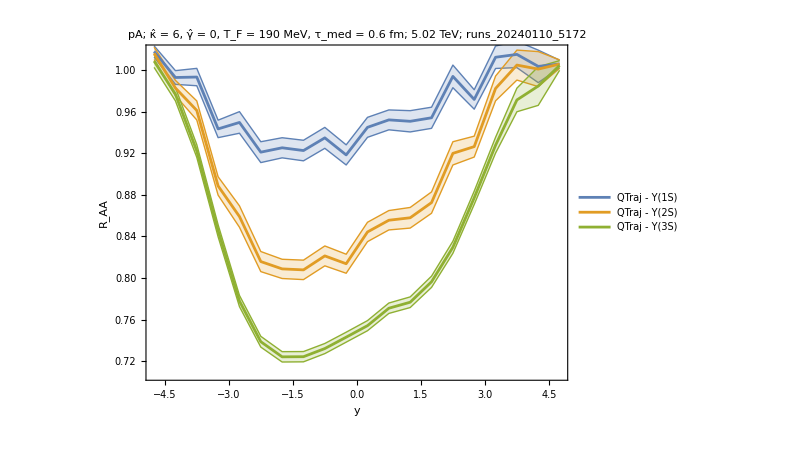

```mathematica
yPlot=ListPlot[{naa1s,naa2s,naa3s},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"y","R_AA"},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,15}}],{Right,Bottom}],PlotRange->All,PlotLabel->labelMap[dataDir]]
```

```mathematica
fileName =dirName<>"/rpavsy.m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
qtrajRPAvsy={naa1s,naa2s,naa3s};
Save[fileName,qtrajRPAvsy]
```